```mathematica
h[z_]:=Style[z,FontFamily->"Times New Roman"];
x=10^23;silva=1925320391606803968923;
Grid[Map[h,{{"Legendre",Round[x/(Log[x]-1.08366)]},{"Chebyshev",Round[x/(Log[x]-1)]},
{"Gauss",Round[LogIntegral[x]]},{"Riemann",Round[RiemannR[x]]},{"π(10^23)",silva}},{2}],Dividers->All,Background->RGBColor[1.,1.,0.8]]
```

Legendre | 1927681221597738565632
Chebyshev | 1924577459166813514800
Gauss | 1925320391614054155139
Riemann | 1925320391607837268776
π(10^23) | 1925320391606803968923

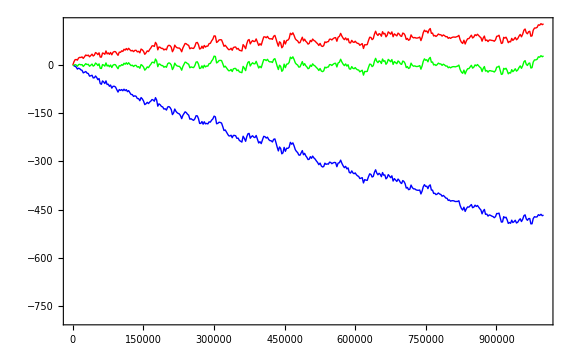

```mathematica
Plot[{LogIntegral[x]-PrimePi[x],RiemannR[x]-PrimePi[x],x/(Log[x]-1)-PrimePi[x]},
{x,2,10^6},MaxRecursion->3,Frame->True,
PlotStyle->{{Thick,Red},{Thick,Green},{Thick,Blue}},ImageSize->Large]
```